For a classical harmonic oscillator with initial conditions (x(0), v(0)) = (0,p/m),

```mathematica
x[t_] := v0/ω Sin[ω t] ;
x[t]
x'[t]
```

(v0 Sin[t ω])/ω

v0 Cos[t ω]

```mathematica
ℒ[t_]:= (1/2)m x'[t]^2-(1/2)m ω^2 x[t]^2
TrigReduce[ℒ[t]]
```

1/2 m v0^2 Cos[2 t ω]

Which accumulates a phase of the form

```mathematica
Integrate[ℒ[t],{t,0,T}]//FullSimplify
```

(m v0^2 Sin[2 T ω])/(4 ω)

If allowed to oscillate until returning to the origin (an integer number of half-periods) then the accumulated phase is zero:

```mathematica
Integrate[ℒ[t],{t,0,π/ω}]
```

0

If we instead introduced a mirror at some variable θ we would get

```mathematica
MirroredPhase = 1/ℏ(Integrate[ℒ[t],{t,0,t2}]+Integrate[ℒ[t],{t,π/ω-t2,π/ω}])
```

(m v0^2 Sin[2 t2 ω])/(2 ω ℏ)

A second beamsplitter pulse would then recombine the paths and produce output from two ports with a phase that is periodic in the delay interval θ,

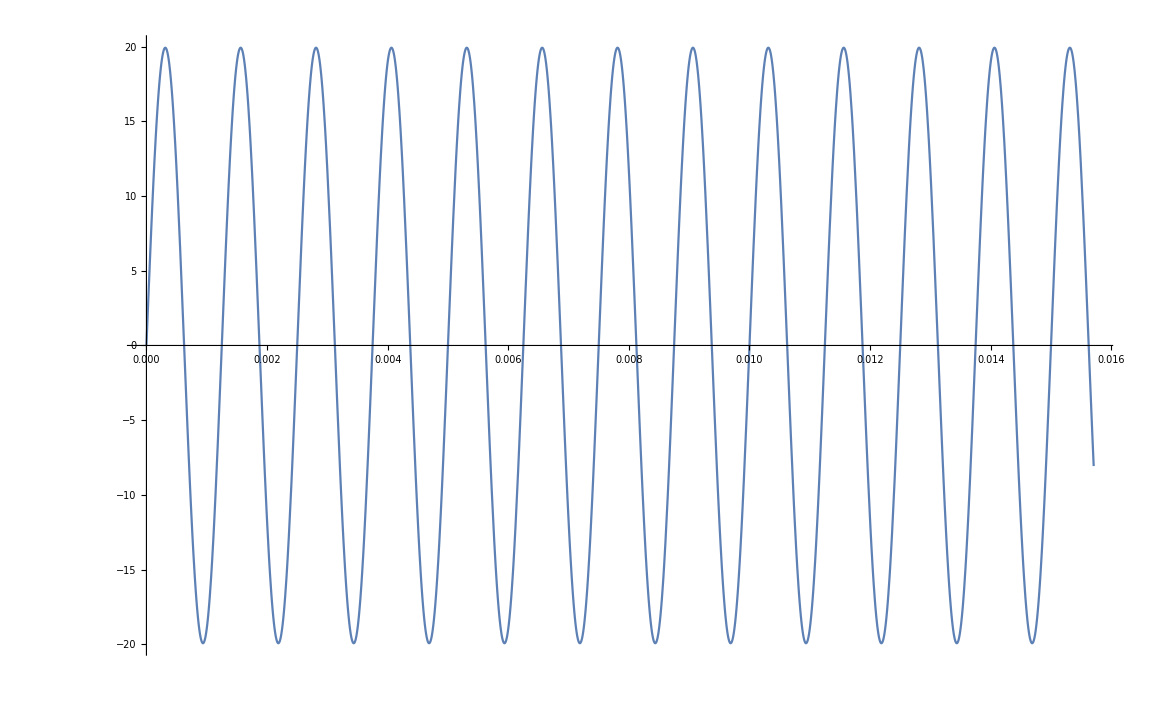

```mathematica
Plot[MirroredPhase/.{v0->.1,m->6.64*10^-27,ω->400*2π,ℏ->6.63*10^-34},{t2,0,2π/400}]
```

Which would produce a phase-modulated interference pattern

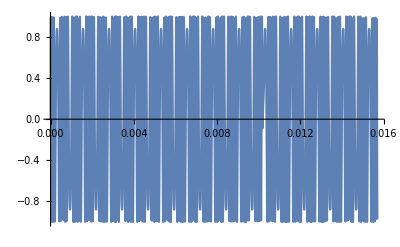

```mathematica
Plot[Sin[MirroredPhase]/.{v0->.1,m->6.64*10^-27,ω->400*2π,ℏ->6.63*10^-34},{t2,0,2π/400}]
```

```mathematica
FullSimplify[D[MirroredPhase,ω]]
```

-(m v0^2 (-2 t2 ω Cos[2 t2 ω]+Sin[2 t2 ω]))/(2 ω^2 ℏ)

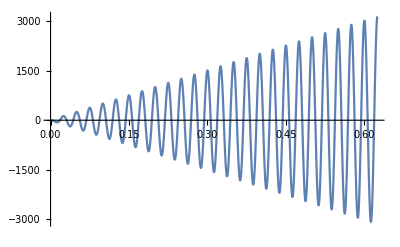

```mathematica
Plot[D[MirroredPhase,ω]/.{v0->.1,m->6.64*10^-27,ℏ->1.05*10^-34}/.{ω->20 2π},{t2,0, (2π)/ω 1/8 100/.{ω->20 2π}}]
```

```mathematica
D[MirroredPhase,ω]/.{v0->.1,m->6.64*10^-27,ℏ->1.05*10^-34,t2-> (2π)/ω 1/8}/.{ω->20 2π}
```

-20.023